```mathematica
wykres[l_,z_]:=Module[{indexin,indexout,retab,imtab,val},

indexin =Position[inltab,l];
indexout =Position[outltab,l];

retab=Table[{funkcjatabin[[indexin[[1,1]],i,1]],funkcjatabin[[indexin[[1,1]],i,2]]},{i,1,Length[funkcjatabin[[indexin[[1,1]]]]]}];
imtab=Table[{funkcjatabin[[indexin[[1,1]],i,1]],funkcjatabin[[indexin[[1,1]],i,3]]},{i,1,Length[funkcjatabin[[indexin[[1,1]]]]]}];

val=Show[ListPlot[{imtab,retab},PlotRange->{{0,40},{-z,z}}],Plot[{funkcjataboutre[[indexout[[1,1]],2]],funkcjataboutim[[indexout[[1,1]],2]]},{r,0,60},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->z]];

Return[val];
];
```

```mathematica
wykres2[l_,z_]:=Module[{indexin,indexout,retab,imtab,val},

indexin =Position[inltab,l];
indexout =Position[outltab,l];

retab=Table[{funkcjatabin[[indexin[[1,1]],i,1]],funkcjatabin[[indexin[[1,1]],i,2]]},{i,1,Length[funkcjatabin[[indexin[[1,1]]]]]}];
imtab=Table[{funkcjatabin[[indexin[[1,1]],i,1]],funkcjatabin[[indexin[[1,1]],i,3]]},{i,1,Length[funkcjatabin[[indexin[[1,1]]]]]}];

val=Show[ListPlot[{imtab,retab},PlotRange->{{0,100},{-z,z}}],Plot[{funkcjataboutre[[indexout[[1,1]],2]],funkcjataboutim[[indexout[[1,1]],2]]},{r,0,1000},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->z]];

Return[val];
];
```

```mathematica
kk =0.650;
```

```mathematica
inpaths=FileNames[StringJoin["z1_k",ToString[SetAccuracy[kk,4]],"_l*"],"/home/mateusz/Documents/cpp/combined_fit/input/"];
outpaths=FileNames[StringJoin["fit_z1_k",ToString[SetAccuracy[kk,4]],"_l*"],"/home/mateusz/Documents/cpp/combined_fit/output/"];
```

```mathematica
infiles=Table[FileNameTake[inpaths[[i]]],{i,1,Length[inpaths]}];
outfiles=Table[FileNameTake[outpaths[[i]]],{i,1,Length[outpaths]}];
```

```mathematica
inltab=Table[ToExpression[StringCases[infiles[[i]],DigitCharacter..][[4]]],{i,1,Length[infiles]}];
outltab=Table[ToExpression[StringCases[outfiles[[i]],DigitCharacter..][[4]]],{i,1,Length[outfiles]}];
```

```mathematica
funkcjatabin=Table[Import[inpaths[[i]]],{i,1,Length[inpaths]}];
 funkcjatabout=Table[Import[outpaths[[i]]],{i,1,Length[outpaths]}];
```

```mathematica
funkcjataboutre=Table[{outltab[[j]],Sum[funkcjatabout[[j,2,i]]*r^outltab[[j]]*(* ((2*funkcjatabout[[j,1,i]])^(-3/2-outltab[[j]])*Gamma[3/2+outltab[[j]]]/2)^(-1/2)* *)Exp[-funkcjatabout[[j,1,i]]*r^2],{i,1,Length[funkcjatabout[[j,2]]]}]},{j,1,Length[funkcjatabout]}];

funkcjataboutim=Table[{outltab[[j]],Sum[funkcjatabout[[j,3,i]]*r^outltab[[j]]*(* ((2*funkcjatabout[[j,1,i]])^(-3/2-outltab[[j]])*Gamma[3/2+outltab[[j]]]/2)^(-1/2)* *)Exp[-funkcjatabout[[j,1,i]]*r^2],{i,1,Length[funkcjatabout[[j,3]]]}]},{j,1,Length[funkcjatabout]}];
```

```mathematica
ll=5;
```

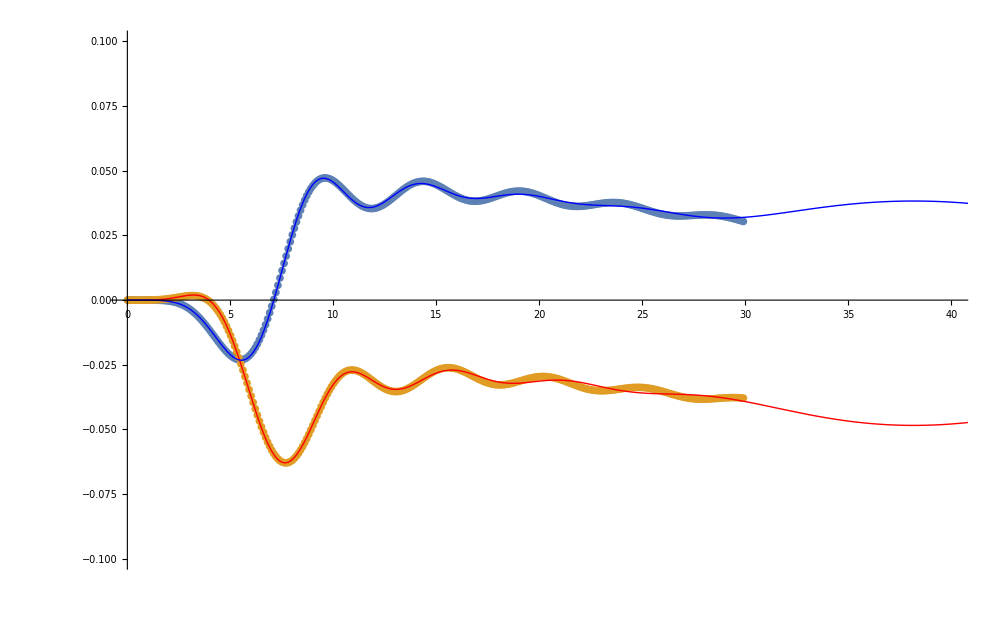

```mathematica
wykres[ll,0.1]
```

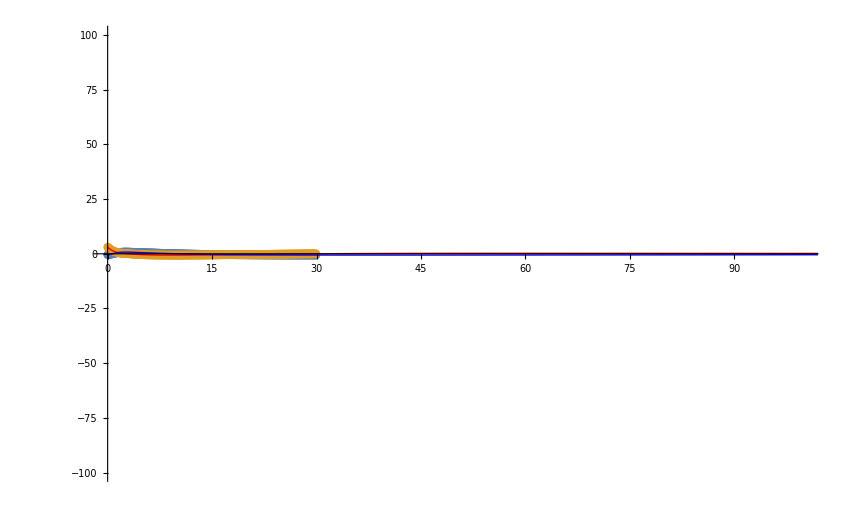

```mathematica
wykres2[ll,100]
```